```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/gregoryridgway/Desktop/Heavy_Ion/SimulatingHydroPlus

TODO:
two snapshots
-phi
-p_(+)
-flow

TODO
1) Following Eqn. for p_(+) we can only include the term proportional to de/dT (take out dphi/dT) and see the effect of Y on c^2
	and plot dp/de # normalized so that the first term is 1, and compare the effect of the other terms.
c_V/(w_(+)β_(+))(dP_(+))/dϵ
1) Plot every individual contribution to (2.7), the dp_(+) equation.
2) plot of which mode is most important (phi_eq * Q^2)

Snapshots

### Constants

Set parameters necessary for interpreting output files properly:

	λM : 		    relaxation rate
	Δ1 and Δ2 : Controls the number of ϕ modes probed
	Nq :                 Total number of ϕ modes

```mathematica
paramList = StringCases[#,x:NumberString:>ToExpression[x]]⟦1⟧&/@(ReadList["params.txt",String]⟦2;;;;2⟧);
λM=paramList⟦-8⟧;(*Relaxation parameter*)
Δ1=80; (*Number of ϕ modes between wavelength 6fm and 0.5fm*)
Δ2=20; (*Number of ϕ modes between wavelength 25fm and 6fm, or 0.5fm and 0fm*)
Nq=Δ1+2*Δ2 (*Total Number of ϕ Modes*);
tc=paramList⟦-7⟧;
{aL,aH,ΔT,ξmax,TLow,THigh}=paramList⟦{-6,-5,-4,-3,-2,-1}⟧;
SciNot[num_]:=Block[{exp=Floor[Log10[num]], dig=0,  remain=0},
dig=Floor[num/10^exp];
remain=num/10^exp-dig ;
If [remain== 0,
Return[ToString[dig]<>"e"<>ToString[exp]],
Return[ToString[dig]<>"."<>StringSplit[
ToString[remain],"."]⟦-1⟧
<>"e"<>ToString[exp]]
]
]

Concat[strings_,nums_]:=StringJoin@Flatten@Transpose[{
strings,SciNot/@nums
}]
str = Concat[{"Tc_","_aL_", "_aH_", "_dT_","_Xm_","_TL_","_TH_"},{tc,aL,aH,ΔT,ξmax,TLow,THigh}];
str
```

Tc_2e-1_aL_1e0_aH_1e0_dT_2e-1_Xm_2e0_TL_8e-1_TH_1.2e0

### Download Files

Defining CreateLists, which takes in a directory where all output files are stored after a simulation, and outputs lists of data indexed by {τ-coordinate, r-coordinate, {r,value}}

#### Functions for Downloading and Processing Output Files

```mathematica
CreateFileNameList[dir_,str_]:=Return[ReadList["!ls ../data/snapshot/"<>dir<>str<>"profile_*",String]];
CreateLists[dir_,verbose_:False] :=Block[{Tfiles,vfiles,edfiles,pfiles,ϕfiles, len, times, Recombine,ϕTimes,ϵlists,Tlists,vlists, plists},
(*List of file names for T, v, ϵ, Subscript[p, (+)], {ϕ(Q)}*)
{Tfiles,vfiles,edfiles,pfiles}=Table[CreateFileNameList[dir,str],
 {str,{"T","v","ed","pplus"}}
];
If[verbose,Print[Length[Tfiles], " ", Length[edfiles]]];
ϕfiles=CreateFileNameList[dir,"Lam"<>ToString[λM]<>"0Phi"];
If[verbose,Print[Length[ϕfiles]]];


len=Length[Tfiles];
If[verbose,Print[StringSplit[Tfiles⟦1⟧,"_"]]];
times=Table[N[(ToExpression[#1]+10^-6 ToExpression[#2])]&@@StringSplit[StringSplit[Tfiles⟦k⟧,"_"]⟦-1⟧,"."]⟦1;;2⟧,{k,len}];

(*Now sort these files in ascending time order*)
If[Position[times,x_/;x>10] ≠  {},
Recombine[L_List]:=(L⟦#⟧&@@@Position[times,x_/;x<10])~Join~(L⟦#⟧&@@@Position[times,x_/;x>10]);
times = Recombine[times];
Tfiles = Recombine[Tfiles];
vfiles = Recombine[vfiles];
edfiles = Recombine[edfiles];
];


ϕTimes = Table[N[(ToExpression[#1]+10^-6 ToExpression[#2])&@@StringSplit[StringSplit[file,"_"]⟦-1⟧,"."]⟦1;;2⟧],{file,ϕfiles}];

If[Position[ϕTimes,x_/;x>10]≠{},
Recombine[L_List]:=(L⟦#⟧&@@@Position[ϕTimes,x_/;x<10])~Join~(L⟦#⟧&@@@Position[ϕTimes,x_/;x>10]);
ϕTimes = Recombine[ϕTimes];
ϕfiles = Recombine[ϕfiles];
pfiles = Recombine[pfiles];
];

(*And create the lists of T, ϵ, and v as a function of r and τ*)
ϵlists = Table[ReadList[file,{Number,Number}],{file,edfiles}];
Tlists= Table[ReadList[file,{Number,Number}],{file,Tfiles}];
vlists = Table[ReadList[file,{Number,Number}],{file,vfiles}];
plists = Table[ReadList[file,{Number,Number,Number}],{file,pfiles}];


Return[{times, ϕTimes, ϵlists, Tlists, vlists,ϕfiles,plists}];
]
```

#### Download Three Sets of Data

Directories where data with a critical point (CP) and backreaction(BR) can be found, with a CP and without BR, and without a CP or BR (respectively)

```mathematica
strBRCP=StringJoin[str,"/with_backreaction/"];
strNoBRCP=StringJoin[str,"/without_backreaction/"];
(*strNoBRNoCP="Tc_2e-1_aL_1e0_aH_1e0_dT_1e-1_Xm_1e0_TL_9e-1_TH_1.1e0/without_backreaction/";*)

{times, ϕTimes, ϵlists, Tlists, vlists,ϕfiles,plists} = CreateLists[strBRCP];
{timesNoBR, ϕTimesNoBR, ϵlistsNoBR, TlistsNoBR, vlistsNoBR,ϕfilesNoBR,plistsNoBR} = CreateLists[strNoBRCP];
(*{times0, ϕTimes0, ϵlists0, Tlists0, vlists0,ϕfiles0,plists0} = CreateLists[strNoBRNoCP];*)
(*{timesI, ϕTimesI, ϵlistsI, TlistsI, vlistsI,ϕfilesI,plistsI} = CreateLists["ideal/"];*)
offset = Length[times]-Length[ϕTimes];
```

```mathematica
Transpose[{times⟦2;;Length[plists]⟧,Table[Max[#2/#1&@@@plists[[i,1;;200,2;;]]],{i,2,Length[plists]}]}]
```

{{1.09865,-0.0246871},{1.1973,-0.0335624},{1.29595,-0.0275588},{1.3946,-0.00891192},{1.49325,0.0203843},{1.5919,0.0578935},{1.69055,0.100581},{1.7892,0.146679},{1.88785,0.194185},{1.9865,0.240585},{2.08515,0.285668},{2.1838,0.328357},{2.28245,0.368461},{2.3811,0.405236},{2.47975,0.438842},{2.5784,0.469164},{2.67705,0.496263},{2.7757,0.520553},{2.87435,0.542113},{2.973,0.56082},{3.07165,0.577248},{3.1703,0.591406},{3.26895,0.603496},{3.30003,-2.78982×10^-11},{3.3676,0.611843},{3.46625,0.620103},{3.5649,0.626559},{3.66355,0.631217},{3.7622,0.634171},{3.86085,0.635532},{3.9595,0.635312},{4.05815,0.633457},{4.1568,0.630018},{4.25545,0.625003},{4.3541,0.618343},{4.45275,0.610015},{4.5514,0.600014},{4.65005,0.588289},{4.7487,0.574656},{4.84735,0.559119},{4.946,0.54146},{5.04465,0.521536},{5.1433,0.499202},{5.24195,0.474294},{5.3406,0.446584},{5.43925,0.415903},{5.5379,0.382221},{5.63655,0.34539},{5.7352,0.305402},{5.83385,0.262397},{5.9325,0.216616},{6.03115,0.168276},{6.1298,0.117886},{6.22845,0.0661655},{6.3271,0.0138481},{6.42575,-0.0382336},{6.5244,-0.0891378},{6.62305,-0.138096},{6.7217,-0.184324},{6.82035,-0.14519},{6.919,-0.255526},{7.01765,-0.24527},{7.1163,-0.275625},{7.21496,-0.133539}}

List of radii for which the fluid is at the critical point

```mathematica
critRlist = Table[
Tlists⟦i,FirstPosition[Tlists⟦i,;;,2⟧,_?(#<.2&)]⟦1⟧,1⟧
,{i,Length[Tlists]}];

critRupper = Table[
Tlists⟦i,FirstPosition[Tlists⟦i,;;,2⟧,_?(#<.22&)]⟦1⟧,1⟧
,{i,Length[Tlists]}];

critRlower = Table[
Tlists⟦i,FirstPosition[Tlists⟦i,;;,2⟧,_?(#<.18&)]⟦1⟧,1⟧
,{i,Length[Tlists]}];

freeze = Table[
Tlists⟦i,FirstPosition[Tlists⟦i,;;,2⟧,_?(#<.155&)]⟦1⟧,1⟧
,{i,Length[Tlists]}];
```

### ϵ, v, and T movies

#### Movie Functions

```mathematica
HydroMovie[dataLists_,ran_,leg_,ylabel_,ϕPlot_,Labeled_]:=Block[{max,numLists=Length[dataLists]},
(*
    numLists:  number of lists to be plotted at once
  dataLists: the lists to be plotted
  ran:       PlotRange
leg:       Legend
ylabel:    label for y axis
*)

max = Min[Length/@dataLists];
(*If[!ϕPlot,
start=1; ts=times,
start=1+offset; ts= ϕTimes];

grids = Table[
{gridlines⟦i,j⟧,styles⟦i⟧},
{j,start,Length[gridlines⟦1⟧]},
{i,Length[gridlines]}
];*)
If[Labeled,
If[!ϕPlot,
Return[
Animate[ListLinePlot[dataLists⟦;;,i⟧,
PlotStyle->{{Blue},{Red,Dashed},{Black},{Black, Dotted}},
PlotLegends->leg,
PlotLabel->Style["τ = "<>ToString[times⟦i⟧]],
GridLines-> {{{critRupper⟦i⟧,Dashed},{critRlist⟦i⟧,Red},{critRlower⟦i⟧,Dashed},{freeze⟦i⟧,Blue}(*,{tmpList⟦i⟧,Blue}*)},None},
PlotRange->ran,
Frame->True,
FrameLabel->{Style["r (fm)",16],Style[ylabel,16]}],{i,1,max,1},AnimationRunning->False]
],
Return[
Animate[ListLinePlot[dataLists⟦;;,i⟧,
PlotStyle->{{Blue},{Red,Dashed},{Orange, Dotted}, {Black,Dotted}},
PlotLegends->leg,
PlotLabel->Style["τ = "<>ToString[ϕTimes⟦i⟧]],
GridLines-> {{{critRupper⟦i+offset⟧,Dashed},{critRlist⟦i+offset⟧,Red},{critRlower⟦i+offset⟧,Dashed},{ϕmaxes⟦i⟧,Blue}},None},
PlotRange->ran,Frame->True,
FrameLabel->{Style["r (fm)",16],Style[ylabel,16]}],{i,1,max,1},AnimationRunning->False]

]
],
If[!ϕPlot,
Return[
Animate[ListLinePlot[dataLists⟦;;,i⟧,
PlotStyle->{{Blue},{Red,Dashed},{Black},{Black, Dotted}},
PlotLegends->leg,
PlotLabel->Style["τ = "<>ToString[times⟦i⟧]],
PlotRange->ran,Frame->True,
FrameLabel->{Style["r (fm)",16],Style[ylabel,16]}],{i,1,max,1},AnimationRunning->False]

],
Return[
Animate[ListLinePlot[dataLists⟦;;,i⟧,
PlotStyle->{{Blue},{Red,Dashed},{Orange, Dotted}, {Black,Dotted}},
PlotLegends->leg,
PlotLabel->Style["τ = "<>ToString[ϕTimes⟦i⟧]],
PlotRange->ran,Frame->True,
FrameLabel->{Style["r (fm)",16],Style[ylabel,16]}],{i,1,max,1},AnimationRunning->False]

]
]
]
]
```

#### Movies

```mathematica
diffListEd=Table[Transpose[{ϵlists⟦k,All,1⟧, ϵlists⟦k,All,2⟧/ϵlistsNoBR⟦k,All,2⟧-1}],{k,1,Min[{Length[ϵlistsNoBR],Length[ϵlists]}]}];
HydroMovie[
{diffListEd},
{{-.5,10},{-.1,.2}},
{"with backreaction","Without Backreaction", "without CP", "Ideal"},
"ϵ",
False,True]
```

```mathematica
HydroMovie[
{ϵlists,ϵlistsNoBR(*,ϵlists0, ϵlistsI*)},
{{-.5,10},{0,.0032}},
{"with backreaction","Without Backreaction", "without CP", "Ideal"},
"ϵ",
False,
True]
```

```mathematica
diffListv=Table[Transpose[{vlists⟦k,All,1⟧, vlists⟦k,All,2⟧/vlistsNoBR⟦k,All,2⟧-1}],{k,2,Min[{Length[vlistsNoBR],Length[vlists]}]}];
HydroMovie[{diffListv},
{{-.5,10},{-.2,.2}},
{"with backreaction","Without Backreaction","No CP","Ideal"},
"v",
False,
True]
```

```mathematica
HydroMovie[{vlists,vlistsNoBR(*,vlists0,vlistsI*)},
{{-.5,10},{0,1}},
{"with backreaction","Without Backreaction","No CP","Ideal"},
"v",
False,
True]
```

```mathematica
HydroMovie[{Abs[plists⟦;;,;;,{1,2}⟧],Abs[plistsNoBR⟦;;,;;,{1,2}⟧](*,Abs[plists0⟦;;,;;,{1,2}⟧]*)},
{{-.5,10},{0,0.01}},
{"with backreaction","Without Backreaction","No CP"},
"-(1-u^τ)∇_r p_(+)/(ϵ+p_(+))",
False,
True]
```

```mathematica
HydroMovie[{vlists,vlistsNoBR,vlists0(*,vlistsI*)},
{{-.5,10},{0,1}},
{"with backreaction","Without Backreaction","No CP","Ideal"},
"v",
False]
```

TODO: gradients of p_(+) vs. gradients of p (to minimize history effects, look earlier
-Switch between EoS’s where c_s^2

```mathematica
HydroMovie[{Abs[plists⟦;;,;;,{1,3}⟧],Abs[plistsNoBR⟦;;,;;,{1,3}⟧](*,Abs[plists0⟦;;,;;,{1,3}⟧]*)},
{{-.5,10},{0,0.005}},
{"with backreaction","Without Backreaction","No CP"},
"-u^τu^r∇_τ p_(+)/(ϵ+p_(+))",
False]
```

```mathematica
HydroMovie[{Abs[plists⟦;;,;;,{1,2}⟧],Abs[plistsNoBR⟦;;,;;,{1,2}⟧](*,Abs[plists0⟦;;,;;,{1,2}⟧]*)},
{{-.5,10},{0,0.02}},
{"with backreaction","Without Backreaction","No CP"},
"-(1-u^τ)∇_r p_(+)/(ϵ+p_(+))",
False]
```

```mathematica
tmp = Transpose[{plists⟦;;,;;,1⟧,plists⟦;;,;;,2⟧-plists⟦;;,;;,3⟧}];
tmpNoBR = Transpose[{plistsNoBR⟦;;,;;,1⟧,plistsNoBR⟦;;,;;,2⟧-plistsNoBR⟦;;,;;,3⟧}];
```

```mathematica
HydroMovie[{plists⟦;;,;;,{1,3}⟧,plistsNoBR⟦;;,;;,{1,3}⟧(*,Abs[plists0⟦;;,;;,{1,3}⟧]*)},
{{-.5,10},{0,0.02}},
{"with backreaction","Without Backreaction","No CP"},
"-u^τu^r∇_τ p_(+)/(ϵ+p_(+))",
False]
```

```mathematica
tmp=Table[Transpose[{plists⟦i,;;,1⟧,plists⟦i,;;,2⟧-plists⟦i,;;,3⟧}],{i,1,Length[plists]}];
tmpNoBR=Table[Transpose[{plistsNoBR⟦i,;;,1⟧,plistsNoBR⟦i,;;,2⟧-plistsNoBR⟦i,;;,3⟧}],{i,1,Length[plistsNoBR]}];
```

```mathematica
HydroMovie[{tmp,tmpNoBR(*,Abs[plists0⟦;;,;;,{1,3}⟧]*)},
{{-.5,10},{0,-0.02}},
{"with backreaction","Without Backreaction","No CP"},
"-u^τu^r∇_τ p_(+)/(ϵ+p_(+))",
False]
```

```mathematica
HydroMovie[
{ϕLists,ϕeqLists},
{{-.5,10},{Min[ϕLists⟦;;,;;,2⟧],Max[ϕLists]}},
{"out-of-equilibrium ϕ","equilibrium ϕ_0"},
"ϕ, λ="<>ToString[Ls⟦mode⟧]<>"fm",
True
]
```

TODO: 
-See if gradient of pressure divided by ϵ+p matches this
-Gluing issues
-non-plus version of above plot
-Look at limits of relaxation rate.

### ϕ movies

Length scales that ϕ modes probe

```mathematica
L0=512*.1973*.25;
L1= 6;
L2=0.5;
Ls=Table[L0-i(L0-L1)/Δ2,{i,0,Δ2-1}]~Join~Table[L1-i(L1-L2)/Δ1,{i,0,Δ1-1}]~Join~Table[L2-i L2/Δ2,{i,0,Δ2-1}];
```

#### Functions for processing ϕ files

```mathematica
CreateϕList[mode_] :=Block[{ϕLists,ϕeqLists, ϕListsNoBR,ϕeqListsNoBR},
Print[Style["Length scale probed, λ = "<>ToString[Ls⟦mode⟧]<>" fm",20]];

ϕeqLists = Table[ReadList["!awk '{print $1, $"<>ToString[3*mode]<>"}' "<>ToString[file],{Number,Number}],{file,ϕfiles}];
ϕLists = Table[ReadList["!awk '{print $1, $"<>ToString[3*mode+1]<>"}' "<>ToString[file],{Number,Number}],{file,ϕfiles}];

ϕeqListsNoBR = Table[ReadList["!awk '{print $1, $"<>ToString[3*mode]<>"}' "<>ToString[file],{Number,Number}],{file,ϕfilesNoBR}];
ϕListsNoBR = Table[ReadList["!awk '{print $1, $"<>ToString[3*mode+1]<>"}' "<>ToString[file],{Number,Number}],{file,ϕfilesNoBR}];

Return[{ϕeqLists,ϕLists,ϕeqListsNoBR,ϕListsNoBR}];
]
```

#### ϕ movies

```mathematica
"Lam"<>ToString[λM]<>"0Phi"
```

Lam200.0Phi

```mathematica
λM=1000;
mode=80;
ϕfilesNoBR=CreateFileNameList[str<>"/without_backreaction/","Lam"<>ToString[λM]<>"Phi"];
ϕeqListsNoBR = Table[ReadList["!awk '{print $1, $"<>ToString[3*mode]<>"}' "<>ToString[file],{Number,Number}],{file,ϕfilesNoBR}];
ϕListsNoBR = Table[ReadList["!awk '{print $1, $"<>ToString[3*mode+1]<>"}' "<>ToString[file],{Number,Number}],{file,ϕfilesNoBR}];
Length[ϕfilesNoBR]
```

41

```mathematica
mode =110;
{ϕeqLists,ϕLists,ϕeqListsNoBR,ϕListsNoBR}=CreateϕList[mode];
```

Length scale probed, λ = 0.275 fm

```mathematica
ϕmaxes=Table[
ϕLists⟦i,Position[ϕLists⟦i,;;,2⟧,_?(#==Max[ϕLists⟦i,;;,2⟧]&)]⟦1,1⟧,1⟧
,{i,Length[ϕLists]}
];
```

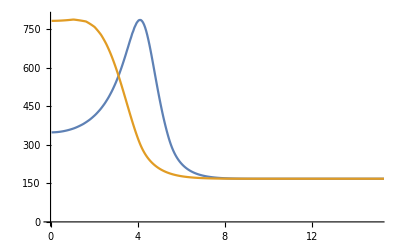

```mathematica
ind=10;
ListLinePlot[{ϕListsNoBR⟦ind⟧,ϕeqListsNoBR⟦ind⟧},PlotRange->{{0,15},{0,800}}]
```

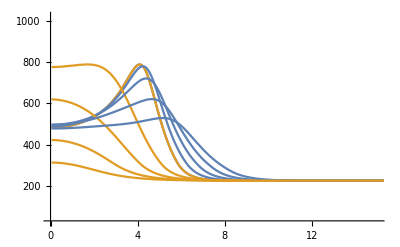

```mathematica
ind=-11;
Show[Table[ListLinePlot[{ϕListsNoBR⟦i⟧,ϕeqListsNoBR⟦i⟧},PlotRange->{{0,15},{26,1020}}],{i,1,40,9}]]
```

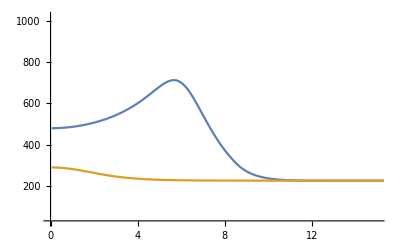

```mathematica
ind=40;
ListLinePlot[{ϕListsNoBR⟦ind⟧,ϕeqListsNoBR⟦ind⟧},PlotRange->{{0,15},{26,1020}}]
```

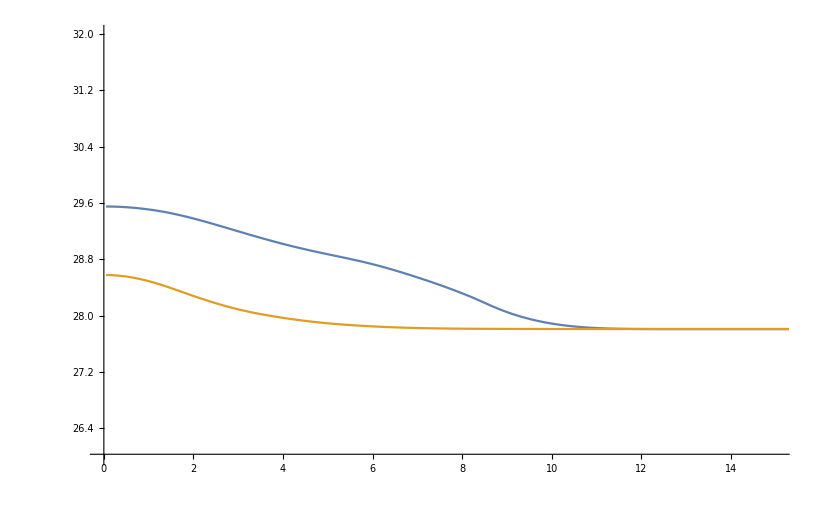

```mathematica
ind=40;
ListLinePlot[{ϕLists⟦ind⟧,ϕeqLists⟦ind⟧},PlotRange->{{0,15},{26,32}}]
```

```mathematica
ind=3;
ListLinePlot[{ϕListsNoBR⟦ind⟧,ϕeqListsNoBR⟦ind⟧},PlotRange->{{0,15},{0,50}}]
```

Part::partw: Part 3 of {} does not exist.

-Graphics-

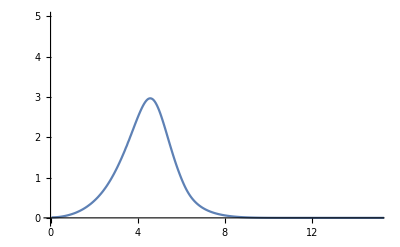

```mathematica
ind=-20;
tmp = Transpose[{ϕListsNoBR⟦ind⟧⟦All,1⟧, ϕListsNoBR⟦ind⟧⟦All,2⟧/ϕeqListsNoBR⟦ind⟧⟦All,2⟧-1}];
ListLinePlot[tmp,PlotRange->{{0,15},{-.1,5}}]
```

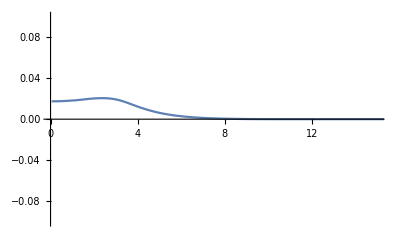

```mathematica
ind=-20;
tmp = Transpose[{ϕListsNoBR⟦ind⟧⟦All,1⟧, ϕListsNoBR⟦ind⟧⟦All,2⟧/ϕeqListsNoBR⟦ind⟧⟦All,2⟧-1}];
ListLinePlot[tmp,PlotRange->{{0,15},{-.1,.1}}]
```

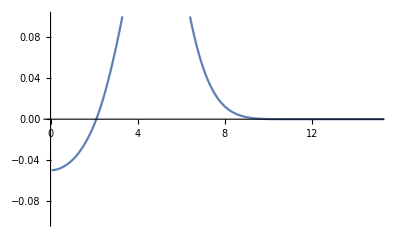

```mathematica
ind=20;
tmp = Transpose[{ϕListsNoBR⟦ind⟧⟦All,1⟧, ϕListsNoBR⟦ind⟧⟦All,2⟧/ϕeqListsNoBR⟦ind⟧⟦All,2⟧-1}];
ListLinePlot[tmp,PlotRange->{{0,15},{-.1,.1}}]
```

```mathematica
ListLinePlot[{ϕListsNoBR⟦;;,1⟧,ϕeqListsNoBR⟦;;,1⟧}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
Animate[ListLinePlot[{ϕListsNoBR⟦i,;;⟧,ϕeqListsNoBR⟦i,;;⟧},
PlotStyle->{{Blue},{Red,Dashed},{Orange, Dotted}, {Black,Dotted}},
PlotRange->{0,800}
(*PlotLegends->leg,
PlotLabel->Style["τ = "<>ToString[ϕTimes⟦i⟧]],
GridLines-> {{{critRupper⟦i+offset⟧,Dashed},{critRlist⟦i+offset⟧,Red},{critRlower⟦i+offset⟧,Dashed},{ϕmaxes⟦i⟧,Blue}},None},
PlotRange->ran,Frame->True,
FrameLabel->{Style["r (fm)",16],Style[ylabel,16]}*)],{i,1,35,1},AnimationRunning->False]
```

```mathematica
HydroMovie[
{ϕLists,ϕeqLists},
{{-.5,10},{Min[ϕLists⟦;;,;;,2⟧],Max[ϕLists]}},
{"out-of-equilibrium","equilibrium"},
"ϕ, λ="<>StringTake[ToString[Ls⟦mode⟧],4]<>"fm",
True,
False
]
```

```mathematica
HydroMovie[
{ϕLists,ϕeqLists},
{{-.5,10},{Min[ϕLists⟦;;,;;,2⟧],Max[ϕLists]}},
{"out-of-equilibrium","equilibrium"},
"ϕ, λ="<>StringTake[ToString[Ls⟦mode⟧],4]<>"fm",
True,
False
]
```

```mathematica
HydroMovie[
{ϕLists,ϕListsNoBR},
{{-.5,10},{Min[ϕLists⟦;;,;;,2⟧],Max[ϕLists]}},
{"ϕ back-reaction","ϕ No Backreaction"},
"ϕ, λ="<>ToString[Ls⟦mode⟧]<>"fm",
True
]
```

HydroMovie[1]
 |  |  |  |

### ϕ contributions

Download ϕ contribution files

```mathematica
ϕContFiles=ReadList["!ls ../data/snapshot/"<>strBRCP<>"phiprofileContribution_*",String];
ϕContributions = 
Table[
Partition[ReadList["! grep '' "<>ToString[file],Number],Nq+1]
,{file,ϕContFiles}];
```

Make a contour plot (radial coordinate vs. λ scale probed) of the change in the entropy due to the presence of the ϕ modes, δs_(+), normalized by the entropy, s, per Q mode.

```mathematica
ConstantArray[ϕContributions⟦tInd,5,1⟧,100]//Dimensions
```

{100}

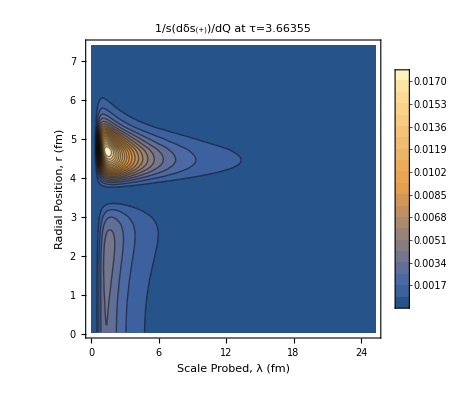

```mathematica
tInd=5;
dQ=Differences[((4Ls)/(.1973))^-1];
dQ={dQ⟦1⟧}~Join~dQ;
(*data=Table[Transpose[{Ls,ConstantArray[ϕContributions⟦tInd,i,1⟧,Nq],Log10[Abs[ϕContributions⟦tInd,i,2;;⟧/dQ]]}],{i,512}];*)
data=Table[Transpose[{Ls,ConstantArray[ϕContributions⟦tInd,i,1⟧,Nq],Abs[ϕContributions⟦tInd,i,2;;⟧/dQ]}],{i,150}];
splots=ListContourPlot[Flatten[data,1],
PlotLegends->Automatic,
FrameLabel->{Style["Scale Probed, λ (fm)",16],
Style["Radial Position, r (fm)",16]},
(*GridLines-> {{{2,Dashed}},{{critRlist⟦tInd⟧,Red},{critRlower⟦tInd⟧,Dashed},{critRupper⟦tInd⟧,Dashed},{freeze⟦tInd⟧,Blue}}},*)
PlotRange->All,
(*GridLines-> {None,{{critRupper⟦tInd+offset⟧,Dashed},{critRlist⟦tInd+offset⟧,Red},{critRlower⟦tInd+offset⟧,Dashed}}},*)
PlotLabel->Style["1/s(dδs_(+))/dQ at τ="<>ToString[ϕTimes⟦tInd⟧],20],
Contours->20]
```

```mathematica
Export["/Users/gregoryridgway/Desktop/Heavy_Ion/plot/movieFrames/aerialView2.png",splots];
```

Scratch

```mathematica
Table[Transpose[{Ls,ConstantArray[ϕContributions⟦tInd,i,1⟧,Nq],Log10[Abs[ϕContributions⟦tInd,i,2;;⟧/dQ]]}],{i,512}];
```

```mathematica
4.8/(.1973*.25)
```

97.3137

TODO: 
-Finish Hydro+_movies.nb
-How to plot all the radii while showing that all of the peaks line up at 2fm?
-probability densities, not probabilities
- (why did without-backreaction crash?)
-What’s with the extra bump at lattice spacing 97, at time 10?

```mathematica
tmp = -ϕContributions⟦10,97,2;;⟧/dQ;
tmp = tmp/Total[tmp];

ListLinePlot[Transpose[{Ls,tmp}],PlotRange->All]
```

Check the validity of the integral (plot this correctly -> no kinks)

```mathematica
(*tmp=Partition[ReadList["! grep '' "<>ToString[ϕContFiles[[-40]]],Number],Nq+1];*)
maxInd=400;
jj=20;

(*norm=Total[Transpose[ϕContributions⟦jj,;;maxInd,2;;⟧]];*)
norm=5;
max3=Log10[Max[Abs[ϕContributions⟦jj,;;maxInd,2;;⟧]]]

conts = Range[-2,0,.2]+max3

ListContourPlot[Log10[Abs[ϕContributions⟦jj,;;maxInd,2;;⟧/norm]],
ColorFunction->"SunsetColors",
Contours->conts,
 DataRange->{{25.4,0},{0,maxInd*.1973*.25}},
 PlotLegends->Automatic,(*BarLegend["SunsetColors",{0,max3/2,max3}],*)
FrameLabel->{Style["λ(fm)",16],Style["r(fm)",16]},
PlotLabel->Style["τ = "<>ToString[ϕTimes⟦jj⟧]<>"fm/c",20]
]
```

-s_(+) relative importance of each mode as a function of time

-p_(+)
-Evolution of hydro variables
-Evolution of ϕ

single-column, not microscopic font

Outline:
-Intro
-Summary of Hydro+
-Model (critical point, EoS, parametrization of relaxation rate)
-figures

Some Checks:
-LAMBDA_M
	-- in comoving coordinates when relaxation goes to zero, you should see a frozen ϕ profile
-check gradient of pressure

Plots for EMMI

```mathematica
HydroMovie[{Abs[plists⟦;;,;;,{1,2}⟧],Abs[plistsNoBR⟦;;,;;,{1,2}⟧](*,Abs[plists0⟦;;,;;,{1,2}⟧]*)},
{{-.5,10},{0,0.01}},
{"with backreaction","Without Backreaction","No CP"},
"-(1-u^τ)∇_r p_(+)/(ϵ+p_(+))",
False,
True]
```

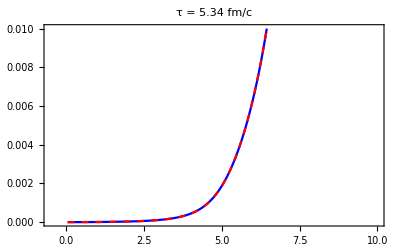

```mathematica
ind=6;
tInd=Table[2+4*i,{i,0,8}]⟦ind⟧;
pplot=ListLinePlot[{Abs[plists⟦tInd,;;,{1,2}⟧],Abs[plistsNoBR⟦tInd,;;,{1,2}⟧]},
PlotLabel->Style["τ = "<>StringTake[ToString[ϕTimes⟦tInd⟧],4]<>" fm/c",20],
PlotStyle->{{Blue},{Red,Dashed}},
(*PlotLegends->{"ϵ","ϵ No BR","v no CP"},*)
(*FrameLabel->{Style["",16],Style["equilibrium",14]},*)
Frame->True,
(*GridLines-> {{{critRupper⟦tInd+24⟧,Dashed},{critRlist⟦tInd+24⟧,Red},{critRlower⟦tInd+24⟧,Dashed},{freeze⟦tInd+24⟧,Blue}(*,{tmpList⟦i⟧,Blue}*)},None},*)
(*PlotRange->{{-.5,10},{0,3}}*)
PlotRange->{{-.5,10},{0,.01}}]

Export["/Users/gregoryridgway/Desktop/Heavy_Ion/plot/movieFrames/pplot"<>ToString[ind]<>".png",pplot];
```

```mathematica
HydroMovie[{Abs[plists⟦;;,;;,{1,2}⟧],Abs[plistsNoBR⟦;;,;;,{1,2}⟧](*,Abs[plists0⟦;;,;;,{1,2}⟧]*)},
{{-.5,10},{0,0.01}},
{"with backreaction","Without Backreaction","No CP"},
"-(1-u^τ)∇_r p_(+)/(ϵ+p_(+))",
False,
True]
```

3.66

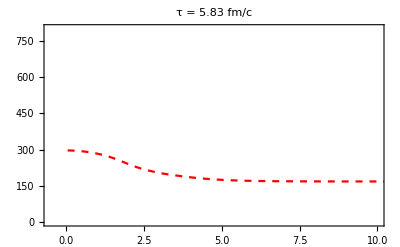

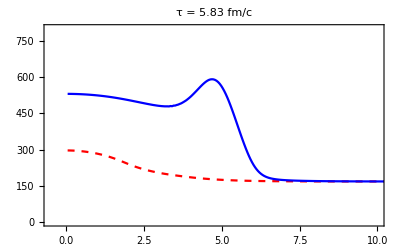

```mathematica
ind=6;
tInd=Table[2+5*i,{i,0,8}]⟦ind⟧;
ϕeq=ListLinePlot[ϕeqLists⟦tInd⟧,
PlotLabel->Style["τ = "<>StringTake[ToString[ϕTimes⟦tInd⟧],4]<>" fm/c",20],
PlotStyle->{Red,Dashed},
(*PlotLegends->{"ϵ","ϵ No BR","v no CP"},*)
(*FrameLabel->{Style["",16],Style["equilibrium",14]},*)
Frame->True,
(*GridLines-> {{{critRupper⟦tInd+24⟧,Dashed},{critRlist⟦tInd+24⟧,Red},{critRlower⟦tInd+24⟧,Dashed},{freeze⟦tInd+24⟧,Blue}(*,{tmpList⟦i⟧,Blue}*)},None},*)
(*PlotRange->{{-.5,10},{0,3}}*)
PlotRange->{{-.5,10},{0,800}}]

ϕnoneq=ListLinePlot[{ϕeqLists⟦tInd⟧,ϕLists⟦tInd⟧},
PlotLabel->Style["τ = "<>StringTake[ToString[ϕTimes⟦tInd⟧],4]<>" fm/c",20],
PlotStyle->{{Red,Dashed},{Blue}},
Frame->True,
(*GridLines-> {{{critRupper⟦tInd+24⟧,Dashed},{critRlist⟦tInd+24⟧,Red},{critRlower⟦tInd+24⟧,Dashed},{freeze⟦tInd+24⟧,Blue}(*,{tmpList⟦i⟧,Blue}*)},None},*)
PlotRange->{{-.5,10},{0,800}}]

Export["/Users/gregoryridgway/Desktop/Heavy_Ion/plot/movieFrames/phieqplot"<>ToString[ind]<>".png",ϕeq];
Export["/Users/gregoryridgway/Desktop/Heavy_Ion/plot/movieFrames/phiplot"<>ToString[ind]<>".png",ϕnoneq];
```

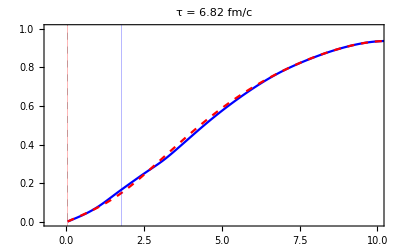

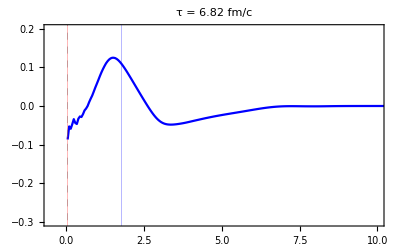

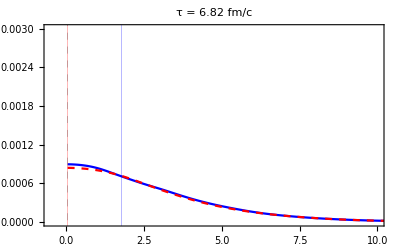

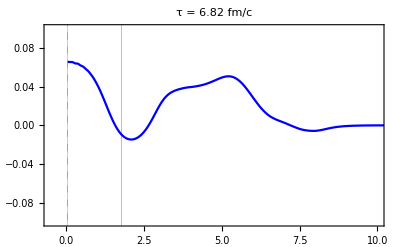

```mathematica
ind=8;
tInd=Table[29+8*(i-3),{i,0,8}]⟦ind⟧;
vplot=ListLinePlot[{vlists⟦tInd⟧,vlistsNoBR⟦tInd⟧},
PlotLabel->Style["τ = "<>StringTake[ToString[times⟦tInd⟧],4]<>" fm/c",20],
PlotStyle->{{Blue},{Red,Dashed}},
Frame->True,
GridLines-> {{{critRupper⟦tInd⟧,Dashed},{critRlist⟦tInd⟧,Red},{critRlower⟦tInd⟧,Dashed},{freeze⟦tInd⟧,Blue}(*,{tmpList⟦i⟧,Blue}*)},None},
PlotRange->{{-.5,10},{0,1}}]

diffvplot=ListLinePlot[{diffListv⟦tInd⟧},
PlotLabel->Style["τ = "<>StringTake[ToString[times⟦tInd⟧],4]<>" fm/c",20],
PlotStyle->{{Blue},{Red,Dashed}},
Frame->True,
GridLines-> {{{critRupper⟦tInd⟧,Dashed},{critRlist⟦tInd⟧,Red},{critRlower⟦tInd⟧,Dashed},{freeze⟦tInd⟧,Blue}(*,{tmpList⟦i⟧,Blue}*)},None},
PlotRange->{{-.5,10},{-0.3,0.2}}]


edplot=ListLinePlot[{ϵlists⟦tInd⟧,ϵlistsNoBR⟦tInd⟧},
PlotLabel->Style["τ = "<>StringTake[ToString[times⟦tInd⟧],4]<>" fm/c",20],
PlotStyle->{{Blue},{Red,Dashed}},
Frame->True,
GridLines-> {{{critRupper⟦tInd⟧,Dashed},{critRlist⟦tInd⟧,Red},{critRlower⟦tInd⟧,Dashed},{freeze⟦tInd⟧,Blue}(*,{tmpList⟦i⟧,Blue}*)},None},
PlotRange->{{-.5,10},{0,.003}}]

diffedplot=ListLinePlot[{diffListEd⟦tInd⟧},
PlotLabel->Style["τ = "<>StringTake[ToString[times⟦tInd⟧],4]<>" fm/c",20],
PlotStyle->{{Blue},{Red,Dashed}},
Frame->True,
GridLines-> {{{critRupper⟦tInd⟧,Dashed},{critRlist⟦tInd⟧,Red},{critRlower⟦tInd⟧,Dashed},{freeze⟦tInd⟧,Blue}(*,{tmpList⟦i⟧,Blue}*)},None},
PlotRange->{{-.5,10},{-0.1,0.1}}]

Export["/Users/gregoryridgway/Desktop/Heavy_Ion/plot/movieFrames/vplot"<>ToString[ind]<>".png",vplot];
Export["/Users/gregoryridgway/Desktop/Heavy_Ion/plot/movieFrames/diffvplot"<>ToString[ind]<>".png",diffvplot];
Export["/Users/gregoryridgway/Desktop/Heavy_Ion/plot/movieFrames/edplot"<>ToString[ind]<>".png",edplot];
Export["/Users/gregoryridgway/Desktop/Heavy_Ion/plot/movieFrames/diffedplot"<>ToString[ind]<>".png",diffedplot];

(*Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/phi2.pdf",vplot]*)

(*pplot=ListLinePlot[{Abs[plists⟦tInd⟧],Abs[plistsNoBR⟦tInd⟧]},
PlotLabel->Style["τ = "<>StringTake[ToString[times⟦tInd⟧],4]<>" fm/c",20],
PlotStyle->{{Blue},{Red,Dashed}},
Frame->True,
PlotRange->{{-.5,10},{0,.3}}]*)
```

Plots for Misha

## v

```mathematica
ind1=30;
times⟦ind1⟧
Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/velocities_early.csv",{vlists⟦ind1⟧,vlistsNoBR⟦ind1⟧,vlists0⟦ind1⟧}]
```

3.7622

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/velocities_early.csv

```mathematica
ind2=50;
times⟦ind2⟧
Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/velocities_late.csv",{vlists⟦ind2⟧,vlistsNoBR⟦ind2⟧,vlists0⟦ind2⟧}]
```

5.7352

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/velocities_late.csv

```mathematica
HydroMovie[{vlists,vlistsNoBR,vlists0},
{{-.5,10},{0,1}},
{"with backreaction","Without Backreaction","No CP","Ideal"},
"v",
False]
```

```mathematica
vlists[[30]]
```

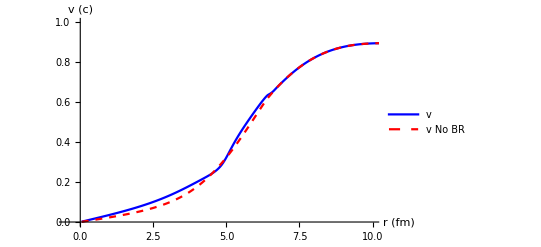

```mathematica
ind1=30;
ListLinePlot[{vlists[[ind1]],vlistsNoBR[[ind1]]},
PlotStyle->{Blue,{Red,Dashed},{Orange,Dotted}},
PlotLegends->{"v","v No BR","v no CP"},
AxesLabel->{"r (fm)","v (c)"},
PlotRange->{{-.5,10},{0,1}}]
```

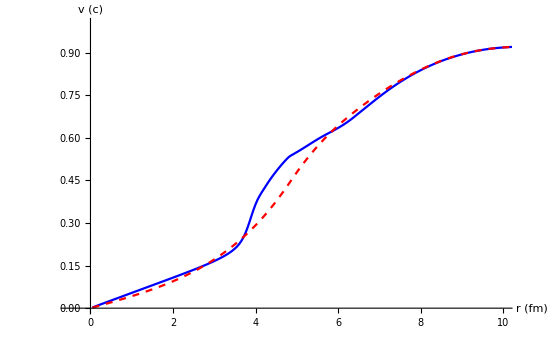

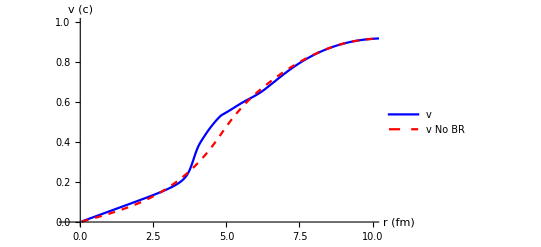

```mathematica
ind1=50;
ListLinePlot[{vlists[[ind1]],vlistsNoBR[[ind1]]},
PlotStyle->{Blue,{Red,Dashed},{Orange,Dotted}},
PlotLegends->{"v","v No BR","v no CP"},
AxesLabel->{"r (fm)","v (c)"},
PlotRange->{{-.5,10},{0,1}}]
```

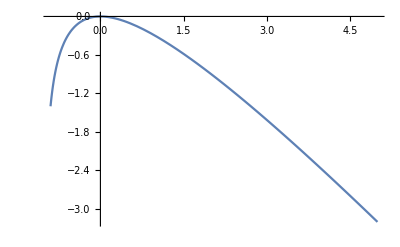

```mathematica
Plot[Log[1+Y]-Y,{Y,-.9,5}]
```

## ϕ

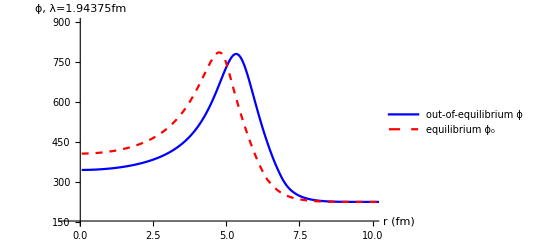

```mathematica
fig1=ListLinePlot[{ϕLists[[6]],ϕeqLists[[6]]},
PlotStyle->{{Blue,Thick},{Red,Dashed}},
PlotLegends->{"out-of-equilibrium ϕ","equilibrium ϕ_0"},
AxesLabel->{Style["r (fm)",16],"ϕ, λ="<>ToString[Ls⟦mode⟧]<>"fm"},
PlotRange->{{-.5,10},{150,900}}]
```

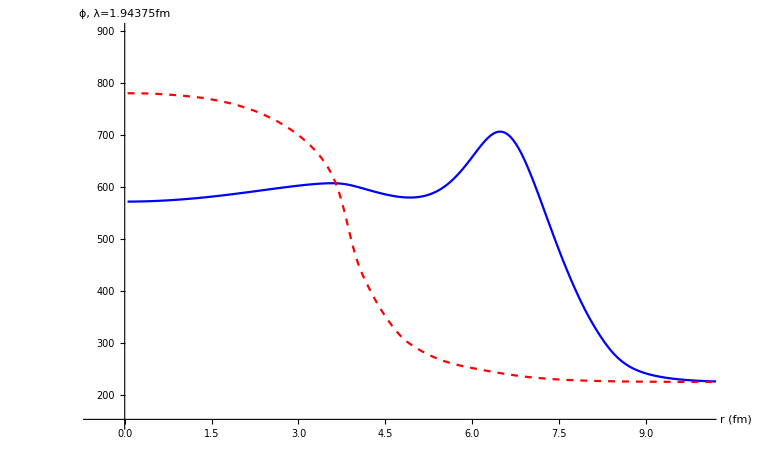

```mathematica
ϕTimes[[6]]
```

3.7622

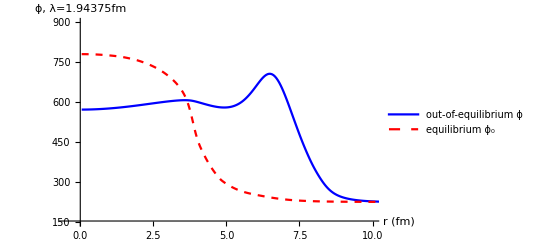

```mathematica
fig2=ListLinePlot[{ϕLists[[26]],ϕeqLists[[26]]},
PlotStyle->{Blue,{Red,Dashed}},
PlotLegends->{"out-of-equilibrium ϕ","equilibrium ϕ_0"},
AxesLabel->{"r (fm)","ϕ, λ="<>ToString[Ls⟦mode⟧]<>"fm"},
PlotRange->{{-.5,10},{150,900}}]
```

```mathematica
Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/early_phi_plot.pdf",fig1]
```

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/early_phi_plot.pdf

```mathematica
Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/late_phi_plot.pdf",fig2]
```

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/late_phi_plot.pdf

```mathematica
ϕTimes[[26]]
```

5.7352

```mathematica
ind1=6;
ϕTimes⟦ind1⟧
Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/phis_early.csv",{ϕLists⟦ind1⟧,ϕeqLists⟦ind1⟧}]
```

3.7622

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/phis_early.csv

```mathematica
ind2=26;
ϕTimes⟦ind2⟧
Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/phis_late.csv",{ϕLists⟦ind2⟧,ϕeqLists⟦ind2⟧}]
```

5.7352

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/phis_late.csv

## ϵ

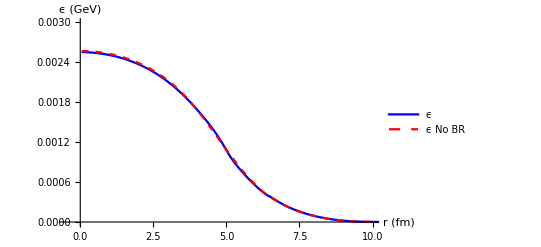

```mathematica
ind1=30;
ListLinePlot[{ϵlists[[ind1]],ϵlistsNoBR[[ind1]]},
PlotStyle->{Blue,{Red,Dashed},{Orange,Dotted}},
PlotLegends->{"ϵ","ϵ No BR","v no CP"},
AxesLabel->{"r (fm)","ϵ (GeV)"},
PlotRange->{{-.5,10},{0,.003}}]
```

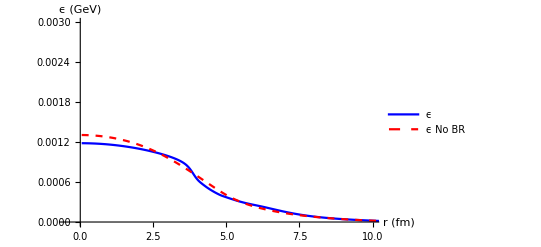

```mathematica
ind1=50;
ListLinePlot[{ϵlists[[ind1]],ϵlistsNoBR[[ind1]]},
PlotStyle->{Blue,{Red,Dashed},{Orange,Dotted}},
PlotLegends->{"ϵ","ϵ No BR","v no CP"},
AxesLabel->{"r (fm)","ϵ (GeV)"},
PlotRange->{{-.5,10},{0,.003}}]
```

```mathematica
ind1=30;
times⟦ind1⟧
Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/ed_early.csv",{ϵlists⟦ind1⟧,ϵlistsNoBR⟦ind1⟧}]
```

3.7622

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/ed_early.csv

```mathematica
ind2=50;
times⟦ind2⟧
Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/ed_late.csv",{ϵlists⟦ind2⟧,ϵlistsNoBR⟦ind2⟧}]
```

5.7352

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Plots_for_Misha/ed_late.csv

Plots for Paper

## ϕ

```mathematica
ϕTimes[[39]]
```

7.01765

```mathematica
xList1=Transpose[{ϕLists[[6,;;,1]],ϕLists[[6,;;,2]]/ϕeqLists[[6,;;,2]]-1}];
xList2=Transpose[{ϕLists[[26,;;,1]],ϕLists[[26,;;,2]]/ϕeqLists[[26,;;,2]]-1}];
xList3=Transpose[{ϕLists[[39,;;,1]],ϕLists[[39,;;,2]]/ϕeqLists[[39,;;,2]]-1}];
```

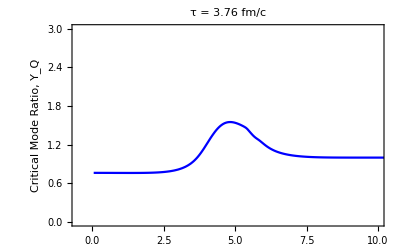

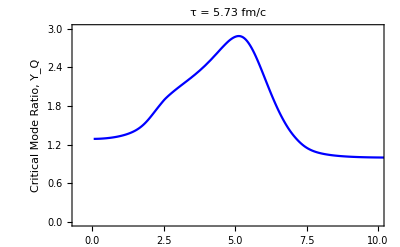

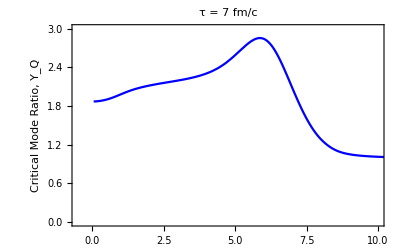

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/phi1.pdf

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/phi2.pdf

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/phi3.pdf

```mathematica
ϕ1=ListLinePlot[xList1,
PlotLabel->Style["τ = 3.76 fm/c",20],
PlotStyle->Blue,
(*PlotLegends->{"ϵ","ϵ No BR","v no CP"},*)
FrameLabel->{Style["",16],Style["Critical Mode Ratio, Y_Q",14]},
Frame->True,
PlotRange->{{-.5,10},{0,3}}]
ϕ2=ListLinePlot[xList2,
PlotLabel->Style["τ = 5.73 fm/c",20],
PlotStyle->Blue,
(*PlotLegends->{"ϵ","ϵ No BR","v no CP"},*)
FrameLabel->{Style["",16],Style["Critical Mode Ratio, Y_Q",14]},
Frame->True,
PlotRange->{{-.5,10},{0,3}}]
ϕ3=ListLinePlot[xList3,
PlotLabel->Style["τ = 7 fm/c",20],
PlotStyle->Blue,
(*PlotLegends->{"ϵ","ϵ No BR","v no CP"},*)
FrameLabel->{Style["",16],Style["Critical Mode Ratio, Y_Q",14]},
Frame->True,
PlotRange->{{-.5,10},{0,3}}]

Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/phi1.pdf",ϕ1]
Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/phi2.pdf",ϕ2]
Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/phi3.pdf",ϕ3]
```

## p

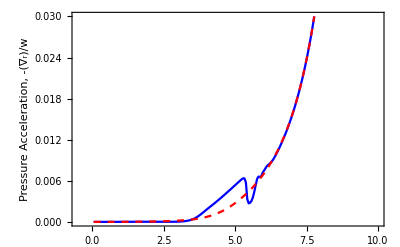

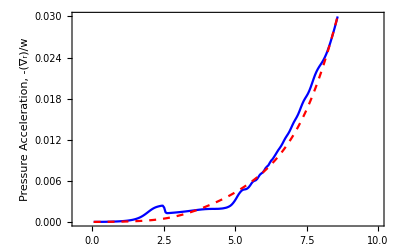

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/p1.pdf

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/p2.pdf

{1}
 |  |  |  |

```mathematica
ind1=30;
ind2=50;
p1=ListLinePlot[{Abs[plists⟦ind1,;;,{1,2}⟧],Abs[plistsNoBR⟦ind1,;;,{1,2}⟧]},
(*PlotLabel->Style["τ = 3.76 fm/c",20],*)
PlotStyle->{Blue,{Red,Dashed},{Orange,Dotted}},
(*PlotLegends->{"ϵ","ϵ No BR","v no CP"},*)
FrameLabel->{Style["",16],Style["Pressure Acceleration, -(∇_r)/w",14]},
Frame->True,
PlotRange->{{-.5,10},{0,.03}}]
p2=ListLinePlot[{Abs[plists⟦ind2,;;,{1,2}⟧],Abs[plistsNoBR⟦ind2,;;,{1,2}⟧]},
(*PlotLabel->Style["τ = 5.73 fm/c",20],*)
PlotStyle->{Blue,{Red,Dashed},{Orange,Dotted}},
(*PlotLegends->{"ϵ","ϵ No BR","v no CP"},*)
FrameLabel->{Style["",16],Style["Pressure Acceleration, -(∇_r)/w",14]},
Frame->True,
PlotRange->{{-.5,10},{0,.03}}]

Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/p1.pdf",p1]
Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/p2.pdf",p2]
```

## v_r

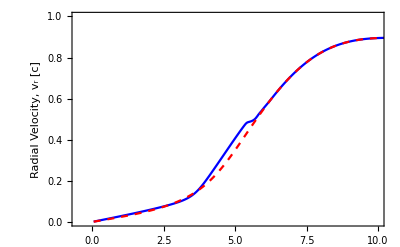

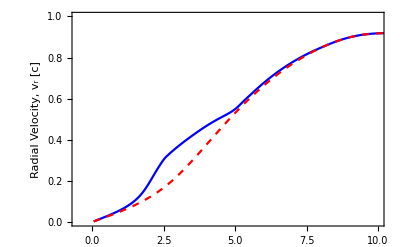

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/v1.pdf

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/v2.pdf

```mathematica
ind1=30;
ind2=50;
v1=ListLinePlot[{vlists⟦ind1⟧,vlistsNoBR⟦ind1⟧},
(*PlotLabel->Style["τ = 3.76 fm/c",20],*)
PlotStyle->{Blue,{Red,Dashed},{Orange,Dotted}},
(*PlotLegends->{"ϵ","ϵ No BR","v no CP"},*)
FrameLabel->{Style["",16],Style["Radial Velocity, v_r [c]",16]},
Frame->True,
PlotRange->{{-.5,10},{0,1}}]
v2=ListLinePlot[{vlists⟦ind2⟧,vlistsNoBR⟦ind2⟧},
(*PlotLabel->Style["τ = 5.73 fm/c",20],*)
PlotStyle->{Blue,{Red,Dashed},{Orange,Dotted}},
(*PlotLegends->{"ϵ","ϵ No BR","v no CP"},*)
FrameLabel->{Style["",16],Style["Radial Velocity, v_r [c]",16]},
Frame->True,
PlotRange->{{-.5,10},{0,1}}]

Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/v1.pdf",v1]
Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/v2.pdf",v2]
```

## ϵ

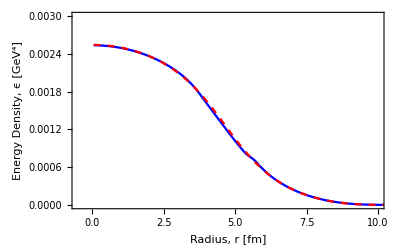

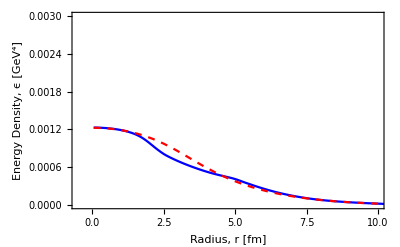

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/ed1.pdf

/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/ed2.pdf

```mathematica
ind1=30;
ind2=50;
ed1=ListLinePlot[{ϵlists⟦ind1⟧,ϵlistsNoBR⟦ind1⟧},
(*PlotLabel->Style["τ = 3.76 fm/c",20],*)
PlotStyle->{Blue,{Red,Dashed},{Orange,Dotted}},
(*PlotLegends->{"ϵ","ϵ No BR","v no CP"},*)
FrameLabel->{Style["Radius, r [fm]",16],Style["Energy Density, ϵ [GeV^4]",16]},
Frame->True,
PlotRange->{{-.5,10},{0,.003}}]
ed2=ListLinePlot[{ϵlists⟦ind2⟧,ϵlistsNoBR⟦ind2⟧},
(*PlotLabel->Style["τ = 5.73 fm/c",20],*)
PlotStyle->{Blue,{Red,Dashed},{Orange,Dotted}},
(*PlotLegends->{"ϵ","ϵ No BR","v no CP"},*)
FrameLabel->{Style["Radius, r [fm]",16],Style["Energy Density, ϵ [GeV^4]",16]},
Frame->True,
PlotRange->{{-.5,10},{0,.003}}]

Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/ed1.pdf",ed1]
Export["/Users/gregoryridgway/Dropbox (MIT)/Hydro+_simulation/Draft/plots/ed2.pdf",ed2]
```

Obsolete

### p, p_(+), D_r p_(+)

Re-organize data

```mathematica
plists = Table[ReadList["!awk '{print $1, $2}' "<>ToString[file],{Number,Number}],{file,pfiles⟦2;;⟧}];
(*plists0 = Table[ReadList["!awk '{print $1, $2}' "<>ToString[file],{Number,Number}],{file,pfiles0⟦5;;⟧}];*)
ppluslists = Table[ReadList["!awk '{print $1, $3}' "<>ToString[file],{Number,Number}],{file,pfiles⟦2;;⟧}];
(*ppluslists0 = Table[ReadList["!awk '{print $1, $3}' "<>ToString[file],{Number,Number}],{file,pfiles0⟦5;;⟧}];*)
(*Dplists = Table[ReadList["!awk '{print $1, $4}' "<>ToString[file],{Number,Number}],{file,pfiles⟦5;;⟧}];
Dppluslists = Table[ReadList["!awk '{print $1, $5}' "<>ToString[file],{Number,Number}],{file,pfiles⟦5;;⟧}];*)
max4 = Max[{Max[plists⟦1,2;;,2⟧],Max[ppluslists⟦1,2;;,2⟧]}];
min = Min[{Min[plists⟦1,2;;,2⟧],Min[ppluslists⟦1,2;;,2⟧]}];
```

p, p_(+), and residual plots

Figure out why p and p_(+) don’t start out exactly the same at the start of the movie

```mathematica
plists//Dimensions
```

{34,512,2}

```mathematica
pAni=Animate[ListLinePlot[{ppluslists⟦i,2;;⟧,plists⟦i,2;;⟧},
PlotStyle->{{Blue,Thick},{Red}},
PlotLabel->Style["p_(+) vs. p, τ = "<>ToString[ϕTimes⟦i⟧],20],PlotRange->{{-.5,15},{min,max4}},
FrameLabel->{Style["r (fm)",16],Style["p (GeV^4)",16]},PlotLegends->{"p_(+)","p"}],{i,1,Length[plists],1},AnimationRate->4,AnimationRunning->False]

(*pAni=Animate[ListLinePlot[{ppluslists⟦i,2;;⟧,ppluslists0⟦i,2;;⟧},
PlotStyle->{{Blue,Thick},{Red}},
PlotLabel->Style["p_(+) vs. p, τ = "<>ToString[ϕTimes⟦i⟧],20],PlotRange->{{-.5,15},{0,max4}},
FrameLabel->{Style["r (fm)",16],Style["p (GeV^4)",16]},PlotLegends->{"p_(+) backreact","p_(+) no backreact"}],{i,1,Length[plists],1},AnimationRate->16,AnimationRunning->False]*)

residualAni=Animate[ListLinePlot[Transpose[{ppluslists⟦i,2;;,1⟧,(ppluslists⟦i,2;;,2⟧-plists⟦i,2;;,2⟧)/plists⟦i,2;;,2⟧}],PlotLabel->Style["residual",20],
PlotStyle->{Blue,Thick},
PlotRange->{{-.5,15},{-.02,.02}},
FrameLabel->{Style["r (fm)",16],Style["(p_(+) - p)/p",6]}],{i,1,Length[plists],1},AnimationRate->4,AnimationRunning->False]
```

Double check that Drp_(+) is computed correctly

```mathematica
fac=5.06842;
Animate[ListLinePlot[{Thread[{ppluslists⟦i,3;;,1⟧,Differences[ppluslists⟦i,2;;,2⟧]/Differences[ppluslists⟦i,2;;,1⟧]}],
Thread[{plists⟦i,3;;,1⟧,Differences[plists⟦i,2;;,2⟧]/Differences[plists⟦i,2;;,1⟧]}],
{#⟦1⟧,#⟦2⟧*fac}&/@Dplists⟦i⟧,
{#⟦1⟧,#⟦2⟧*fac}&/@Dppluslists⟦i⟧},
PlotLabel->Style["Numerical Drp_(+) vs. Drp, Analytic τ = "<>ToString[ϕTimes⟦i⟧],18],
PlotStyle->{{Blue,Thick},{Blue,Dashed,Thick},{Green, Dashed},{Green}},
(*PlotRange->{{-.5,15},{-.0015,.0001}},*)
FrameLabel->{Style["r (fm)",16],Style["Drp",6]},
PlotLegends->{"Numerical Drp_(+)","Numerical Drp", "Drp", "Drp_(+)"}],{i,1,Length[ppluslists],1},AnimationRunning->False,AnimationRate->16]
```